# Exact Diagonalization

```mathematica
(fitresultlist[[2]])["ParameterTable"][[1,1,3,3]]
```

0.0791444

```mathematica
SxHamfixhJSpinSetsHighLowED[TinJlist_,hinJlist_,Jbarstr_,beginSteplist_,endSteplist_,dir_,showfit_,nt_,stdJ_,plotdown_,plotup_,plotleft_,plotright_,fontsize_,loworhigh_]:=(

(*Jbarstr=StringReplace[ToString[NumberForm[Jbar,{2,2}]],"."->"_"]*)
(*Δt=Λtscale/nt//N;*)
tJlist=Import[StringJoin[NotebookDirectory[],dir,"/","t_list.csv"]][[;;,1]];
Sxaver=Import[StringJoin[NotebookDirectory[],dir,"/","Sx_aver.csv"]]//Transpose;
flist=Import[StringJoin[NotebookDirectory[],dir,"/","f_arr.csv"]];

(*Table[Print[StringJoin[NotebookDirectory[],dir,"/","Jbar"<>Jbar<>"/","betaJ"<>betaJlist[[i]]<>"_hinJ"<>hinJlist[[j]],"/","Sx.csv"]],{i,1,betaJnum},{j,1,hinJnum}];*)
(*beginStep=2001;
endStep=3000;*)
setlen=Length[Sxaver];

If[loworhigh,fitresultlist=Table[FindFit[Thread[{Table[tJlist[[i]],{i,beginSteplist[[k]],beginSteplist[[k]]+400}],Sxaver[[k,beginSteplist[[k]];;beginSteplist[[k]]+400]]}],cc*Sin[aa*t]+1.0,{aa,bb,cc,dd},t],{k,1,setlen}];

funcFit=Table[(cc*Sin[aa*t]+1.0)/.fitresultlist[[j]],{j,1,setlen}];
,
fitresultlist=Table[NonlinearModelFit[Thread[{Table[tJlist[[i]],{i,beginSteplist[[k]],endSteplist[[k]]}],Sxaver[[k,beginSteplist[[k]];;endSteplist[[k]]]]}],(cc*Cos[aa*t+dd]*Exp[-t*bb]),{aa,bb,cc,dd},t],{k,1,setlen}];


funcFit=Table[((cc*Cos[(aa)*t+dd]*Exp[-t*bb])/.(fitresultlist[[j]]["BestFitParameters"]))/Sxaver[[j,1]]//FullSimplify,{j,1,setlen}];

(*funcFit=Table[(1*Cos[aa*t]*Exp[-t*bb]+ee)/.(fitresultlist[[j]]["BestFitParameters"]),{j,1,Length[Sxlist]}];*)
];
(*Print["Frequecy list: ",omegalist];
Print["Frequecy Standard Error list: ",omegaStdErr];*)
omegaStdErr=Table[(fitresultlist[[j]])["ParameterTable"][[1,1,2,3]],{j,1,setlen}];
decayStdErr=Table[(fitresultlist[[j]])["ParameterTable"][[1,1,3,3]],{j,1,setlen}];
omegalist=Abs[aa]/.(Table[(fitresultlist[[j]]["BestFitParameters"]),{j,1,setlen}]);
decaylist=Abs[bb]/.(Table[(fitresultlist[[j]]["BestFitParameters"]),{j,1,setlen}]);

data=Table[Thread[{tJlist,(Sxaver⟦k,;;⟧/Sxaver[[k,1]])}],{k,1,setlen}];
Sxdata=Table[data[[k,;;,2]],{k,1,setlen}];
timedata=data[[1,;;,1]];
Export[FileNameJoin[{NotebookDirectory[],"EDSx.mat"}],Sxdata];
Export[FileNameJoin[{NotebookDirectory[],"EDTime.mat"}],timedata];

fig1=ListLinePlot[data,PlotRange->{{plotleft,plotright},{plotdown,plotup}},
LabelStyle->{FontFamily->"Arial",fontsize,GrayLevel[0]},
(*PlotLegends->Placed[LineLegend[Table["J̄="<>ToString[Jbarlist[[i]]],{i,1,Jbarlen}],Spacings->0.05,(*LegendLabel->"label",*)LegendFunction->(Framed[#,RoundingRadius->3]&),LegendMargins->3],legendplace]*)
(*PlotLegends->Table["f="<>ToString[flist[[i]]],{i,1,setlen}],*)
(*,PlotStyle->Directive[Dashed,Thickness[0.008]]*)
PlotTheme->{"Scientific","SansLabels"}
,ImageSize-> Medium,
GridLines->{{tJlist[[beginSteplist[[1]]]]},{}},
(*PlotLabel->  "α="<>ToString[alpha]<>", J̄/J="<>StringReplace[Jbar,"_"->"."]<>", h/J="<>StringReplace[hinJlist[[1]],"_"->"."],*)
FrameLabel->{{"m(t)/m(0)",None},{"tJ",None}},
LabelStyle->{FontFamily->"Arial",fontsize,GrayLevel[0]},FrameStyle->{{Directive[Black,fontsize],Directive[Black,fontsize]},{Directive[Black,fontsize],Directive[Black,fontsize]}},
FrameTicksStyle->{{Style[fontsize,GrayLevel[0]],None},{Style[fontsize,GrayLevel[0]],None}},Frame->{{True,True},{True,True}},FrameTicks->{{All,None},{All,None}},
LabelStyle->{FontFamily->"Arial",fontsize,GrayLevel[0]},PerformanceGoal->"Quality"
(*PlotLabel->"T/J="<>ToString[TinJlist[[1]]]<>",h/J="<>ToString[hinJlist[[1]]]*)
(*Epilog->{Inset[Style["Δ="<>ToString[alpha]<>",βJ="<>ToString[betaJ]<>",h/J="<>ToString[hinJ],epilogfont],Scaled[annotationplace]]}*)
(*Epilog->{Inset[Style["Here",20],Scaled[{1/2,1-1/8}]]}*)];
fig2=Plot[funcFit,{t,tJlist[[beginSteplist[[1]]]],tJlist[[endSteplist[[-1]]]]},PlotRange->{{0,5},{All,All}},PlotStyle->Dashed,PlotLegends->funcFit,PlotTheme->"Scientific"];
figlist=Show[fig1,fig2,ImageSize->Large];
Return[figlist];
);
```

# Draft 2023/07/17

NonlinearModelFit::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

General::stop: 在本次计算中，NonlinearModelFit::cvmit 的进一步输出将被抑制.

General::munfl: Exp[-9912.54] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: Exp[-10899.] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: Exp[-724.649] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::stop: 在本次计算中，General::munfl 的进一步输出将被抑制.

{{{1.1282×10^-8,5.70875×10^-9,5.64216×10^-9,2.85496×10^-9},{0.0151876,0.0855518,0.292992,0.0745769},{0.027535,0.262708,0.355997,0.0679146},{0.0415597,0.600146,0.331589,0.047545},{0.0536195,1.23837,0.178936,0.01712},{0.978689,1.42274,0.00498827,0.0146682},{1.59129,1.48056,0.0105106,0.0208391},{2.0327,1.54441,0.0186858,0.0281906},{2.38974,1.63644,0.0249535,0.0328922},{2.63606,1.86277,0.0254027,0.0343678},{2.85156,2.23599,0.0272978,0.0426991},{3.04191,2.59729,0.0263423,0.0466487},{3.18684,2.89531,0.0244546,0.0471696}},{{2.78462×10^-8,2.54416×10^-8,7.66984×10^-10,7.00755×10^-10},{0.0440201,0.0529994,0.041536,0.0684203},{0.0227614,0.239527,0.355678,0.0677178},{0.0294386,0.563442,0.44122,0.0522898},{0.0392995,1.21442,0.325714,0.024562},{0.949176,1.50114,0.0071356,0.0175122},{1.6057,1.50321,0.0112974,0.0228988},{2.03724,1.52825,0.0181998,0.0268102},{2.38827,1.63139,0.0230389,0.030103},{2.63508,1.86223,0.0234815,0.031775},{2.85114,2.23666,0.0253595,0.039693},{3.04179,2.5982,0.0245746,0.043545},{3.18685,2.89557,0.0226567,0.0437081}},{{6.19015×10^-9,4.93066×10^-9,3.09508×10^-9,2.46533×10^-9},{0.0323333,0.0566495,0.057002,0.0612623},{0.0294583,0.216536,0.23133,0.0711096},{0.0268031,0.525613,0.471001,0.0602694},{0.0265457,1.18723,0.608796,0.0331444},{0.928023,1.55141,0.00958073,0.0209188},{1.60937,1.49995,0.0109922,0.0221673},{2.03661,1.52581,0.0170026,0.0249046},{2.38796,1.63171,0.0215344,0.0281678},{2.63492,1.86431,0.0222204,0.0301108},{2.85142,2.2378,0.0239604,0.0375321},{3.04189,2.59842,0.0230647,0.0408752},{3.18687,2.89559,0.0211906,0.0408801}},{{9.82232×10^-8,9.01069×10^-8,2.32551×10^-9,2.13336×10^-9},{0.0339236,0.0440874,0.0291615,0.0570781},{0.0439976,0.18881,0.124,0.0802769},{0.0212789,0.487644,0.596155,0.073396},{0.0290256,1.15889,0.658557,0.0417287},{0.91647,1.578,0.0116404,0.0239134},{1.60957,1.49741,0.0104267,0.0209159},{2.03633,1.52573,0.0160186,0.023471},{2.38814,1.63391,0.0205454,0.0269156},{2.63562,1.86546,0.0212413,0.0288093},{2.85154,2.23784,0.0226756,0.0355203},{3.0419,2.5984,0.0217462,0.0385379},{3.18687,2.89558,0.0199842,0.0385524}},{{4.50918×10^-9,1.47418×10^-9,5.50868×10^-10,1.80094×10^-10},{0.0327091,0.0319571,0.00841261,0.0541902},{0.0504129,0.157559,0.0743734,0.101472},{0.0164426,0.447999,0.810627,0.0979044},{0.0263698,1.13327,0.811806,0.0493463},{0.912131,1.58874,0.0128659,0.0258088},{1.6094,1.49662,0.00990379,0.0198361},{2.03616,1.52646,0.0152684,0.0223871},{2.38895,1.63496,0.0198043,0.0259686},{2.63577,1.86534,0.0202551,0.0274693},{2.85154,2.23779,0.0215206,0.0337099},{3.04189,2.59839,0.0206267,0.0365539},{3.18687,2.89557,0.0189643,0.0365848}},{{1.59918×10^-10,1.20272×10^-10,1.0527×10^-8,7.9172×10^-9},{0.0198644,0.0486754,0.0543109,0.0497825},{0.0417943,0.134532,0.0533842,0.155061},{0.0146773,0.402798,1.05914,0.163723},{0.0236487,1.11169,0.971659,0.0554399},{0.911283,1.59167,0.0133176,0.0265547},{1.60926,1.49642,0.00945754,0.0189388},{2.03639,1.5272,0.0146728,0.0215287},{2.38915,1.63477,0.0190213,0.0249382},{2.63574,1.86524,0.0193424,0.0262293},{2.85154,2.23779,0.0205158,0.0321359},{3.04189,2.59839,0.0196603,0.0348412},{3.18687,2.89557,0.0180758,0.0348709}},{{1.97835×10^-9,1.61879×10^-9,2.74013×10^-9,2.24211×10^-9},{0.0203632,0.0430728,0.037943,0.0482906},{0.0224489,0.119293,0.00741679,0.465935},{4.70653×10^-10,0.302832,49229.3,247722.},{0.0219526,1.09471,1.09041,0.0598828},{0.911451,1.59191,0.0132865,0.0264871},{1.6092,1.4965,0.00907281,0.0181709},{2.03656,1.52735,0.0141308,0.0207365},{2.38912,1.63465,0.0182391,0.0239099},{2.63572,1.86523,0.0185427,0.0251448},{2.85154,2.23779,0.0196435,0.0307697},{3.04189,2.59839,0.0188184,0.0333493},{3.18687,2.89557,0.0173014,0.033377}},{{1.10248×10^-8,9.60223×10^-9,7.3092×10^-10,6.36605×10^-10},{0.0167514,0.0427626,0.0441472,0.0472824},{3.1074×10^-10,0.118874,273026.,123686.},{3.34264×10^-9,0.300149,10253.6,39912.1},{0.017998,1.08236,1.35877,0.0628255},{0.911692,1.59163,0.0130272,0.0259895},{1.60919,1.49661,0.00873126,0.0174891},{2.0366,1.52728,0.0136174,0.0199815},{2.3891,1.63464,0.0175295,0.0229795},{2.63572,1.86525,0.017835,0.0241855},{2.85154,2.2378,0.0188843,0.0295804},{3.04189,2.59839,0.0180801,0.0320409},{3.18687,2.89557,0.0166184,0.0320594}},{{1.64687×10^-8,1.31642×10^-8,4.33822×10^-10,3.46774×10^-10},{0.0188239,0.0341793,0.0180251,0.0482565},{2.56453×10^-10,0.118179,294345.,133959.},{2.45813×10^-10,0.297445,184660.,594261.},{0.0161101,1.07362,1.53122,0.0645849},{0.911829,1.59142,0.0126856,0.0253213},{1.6092,1.49666,0.00842206,0.0168706},{2.03658,1.52723,0.0131401,0.0192803},{2.3891,1.63465,0.016901,0.0221558},{2.63572,1.86525,0.0171918,0.0233132},{2.85154,2.2378,0.0182006,0.0285094},{3.04189,2.59839,0.0174252,0.0308803},{3.18687,2.89557,0.016011,0.0308876}},{{6.70071×10^-8,1.24803×10^-7,1.22869×10^-9,2.2885×10^-9},{0.0160235,0.0346389,0.0230767,0.0494812},{4.55101×10^-10,0.117429,150226.,71965.3},{9.78878×10^-10,0.294807,42749.2,139594.},{0.0156417,1.06767,1.57869,0.065496},{0.911887,1.59131,0.0123282,0.0246139},{1.60921,1.49667,0.0081409,0.0163076},{2.03658,1.52722,0.012703,0.0186386},{2.3891,1.63466,0.0163355,0.0214146},{2.63572,1.86525,0.0166063,0.0225192},{2.85154,2.2378,0.0175807,0.0275385},{3.04189,2.59839,0.0168316,0.0298283},{3.18687,2.89557,0.0154671,0.0298382}},{{4.68088×10^-8,2.34451×10^-8,8.82618×10^-10,4.42076×10^-10},{0.00961066,0.0156336,0.066822,0.0556653},{1.84155×10^-11,0.116645,3.68953×10^6,1.5211×10^6},{1.35826×10^-9,0.29228,29145.,95765.7},{0.0159312,1.06372,1.54423,0.0658173},{0.911908,1.59127,0.0119813,0.0239236},{1.60921,1.49667,0.00788561,0.0157961},{2.03657,1.52723,0.0123018,0.0180501},{2.3891,1.63466,0.0158174,0.0207355},{2.63572,1.86525,0.0160765,0.0218009},{2.85154,2.2378,0.0170215,0.0266625},{3.04189,2.59839,0.0162968,0.0288805},{3.18687,2.89557,0.0149765,0.028892}},{{4.9906×10^-9,3.83271×10^-9,3.55369×10^-10,2.72918×10^-10},{0.00970005,0.018597,0.0538295,0.0609184},{6.81906×10^-14,0.115839,1.09531×10^9,1.6873×10^8},{2.64829×10^-9,0.28989,13949.6,46640.2},{0.0163925,1.06116,1.49046,0.0657301},{0.911915,1.59125,0.0116549,0.0232728},{1.60921,1.49666,0.00765282,0.0153297},{2.03657,1.52723,0.0119334,0.0175095},{2.3891,1.63466,0.0153432,0.0201138},{2.63572,1.86525,0.0155959,0.021149},{2.85154,2.2378,0.016514,0.0258676},{3.04189,2.59839,0.015809,0.0280162},{3.18687,2.89557,0.0145383,0.0280464}},{{4.17987×10^-8,4.03723×10^-8,7.30752×10^-10,7.05814×10^-10},{0.00837943,0.0201886,0.0588274,0.0707259},{1.52099×10^-10,0.115023,372212.,207200.},{5.16774×10^-9,0.287652,6976.43,23218.9},{0.0167034,1.05955,1.44934,0.0653576},{0.911916,1.59125,0.0113519,0.0226679},{1.60921,1.49666,0.00743797,0.0148993},{2.03657,1.52723,0.0115956,0.0170139},{2.3891,1.63466,0.014909,0.0195445},{2.63572,1.86525,0.0151591,0.0205567},{2.85154,2.2378,0.0160473,0.0251366},{3.04189,2.59839,0.0153617,0.0272234},{3.18687,2.89557,0.0141324,0.0272636}}}

NonlinearModelFit::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

General::stop: 在本次计算中，NonlinearModelFit::cvmit 的进一步输出将被抑制.

General::munfl: Exp[-9702.63] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: Exp[-9878.1] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: Exp[-1534.41] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::stop: 在本次计算中，General::munfl 的进一步输出将被抑制.

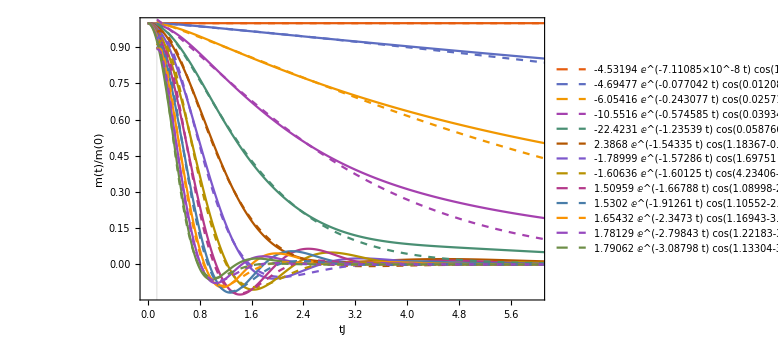

```mathematica
hlist={10.0};
Tlist=hlist/0.4;
fontsize=14;
dirname="rs_Sx_draftRandomf_dynamics_20230716_rhox";
flist=Import[StringJoin[NotebookDirectory[],dirname,"\\","f_arr.csv"]];
setlen=Length[flist];
fitSxEDfreqDecaylist=Flatten[Table[SxHamfixhJSpinSetsHighLowED[Tlist,hlist,"0_0",Table[k,{i,1,setlen}],Table[j,{i,1,setlen}],dirname,False,2000,1,All,All,0,6.0,fontsize,False];Thread[{omegalist,decaylist,omegaStdErr,decayStdErr}],{j,300,900,50},{k,1,1,8}],1]

fitendlist={300,300,300,300,300,300,300,300,300,300,300,900,300,900,900,900,900,900,900,900};
fitbeginlist={15,15,15,15,15,15,15,15,15,15,15,15,10,10,10,15,15,15,15,15};
SxHamfixhJSpinSetsHighLowEDfigDraft=SxHamfixhJSpinSetsHighLowED[Tlist,hlist,"0_0",fitbeginlist,fitendlist,dirname,False,2000,1,All,All,0,6.0,fontsize,False]
```

```mathematica
omegaStdErr
```

{4.96963×10^-10,0.331575,0.372957,0.379394,0.214397,0.00507004,0.0118626,0.0221129,0.0300678,0.0312618,0.0360473,0.0207622,0.0298718}

```mathematica
Export[FileNameJoin[{"C:\\Users\\tgzhou\\Dropbox\\Project\\NMR_wormhole\\draft\\Universal Aspect of Relaxation Dynamics in Random Spin Models\\supp","figRandomED.pdf"}],SxHamfixhJSpinSetsHighLowEDfigDraft]
```

C:\Users\tgzhou\Dropbox\Project\NMR_wormhole\draft\Universal Aspect of Relaxation Dynamics in Random Spin Models\supp\figRandomED.pdf

```mathematica
(*Prepare Data*)
fitSxEDfreqlist=fitSxEDfreqDecaylist[[;;,;;,1]];
fitSxEDDecaylist=fitSxEDfreqDecaylist[[;;,;;,2]];
fitSxEDfreqlistStdErr=Mean[fitSxEDfreqDecaylist[[;;,;;,3]]];
fitSxEDDecaylistStdErr=Mean[fitSxEDfreqDecaylist[[;;,;;,4]]];
statData=Table[{Mean[fitSxEDfreqlist[[;;,i]]],Min[fitSxEDfreqlist[[;;,i]]],Max[fitSxEDfreqlist[[;;,i]]]},{i,1,Length[flist]}];
(*After J rescale*)
dataFreqEDplot=Table[Around[statData[[i,1]],{statData[[i,2]]-statData[[i,1]],statData[[i,3]]-statData[[i,1]]}],{i,1,Length[flist]}]/Jrescale//FullSimplify
statData=Table[{Mean[fitSxEDDecaylist[[;;,i]]],Min[fitSxEDDecaylist[[;;,i]]],Max[fitSxEDDecaylist[[;;,i]]]},{i,1,Length[flist]}];
dataDecayEDplot=Table[Around[statData[[i,1]],{statData[[i,2]]-statData[[i,1]],statData[[i,3]]-statData[[i,1]]}],{i,1,Length[flist]}]/Jrescale

(*Plot*)
flist={{-0.4,0.2,0.2},{-0.35,0.15,0.2},{-0.3,0.1,0.2},{-0.25,0.05,0.2},{-0.2,0.0,0.2},{-0.15,-0.05,0.2},{-0.1,-0.1,0.2},{-0.05,-0.15,0.2},{0.0,-0.2,0.2},{0.05,-0.25,0.2},{0.1,-0.3,0.2},{0.15,-0.35,0.2},{0.2,-0.4,0.2}}*Jrescale;
Jrescale=5.0;
xilist=flist/Jrescale;
xixarr=xilist[[;;,1]];
freqtheory=Table[√(-ξ1^2+ξ2^2-4 ξ2 *ξ3+ξ3^2)/.{ξ1->xilist[[i,1]],ξ2->xilist[[i,2]],ξ3->xilist[[i,3]]},{i,1,Length[xilist]}]//N//Re;
Bpoly=(If[(-ξ1^2+ξ2^2-4 ξ2 *ξ3+ξ3^2)>0,√(ξ1^2+ξ2^2+ξ3^2),√(ξ1^2+ξ2^2+ξ3^2)-√(-(-ξ1^2+ξ2^2-4 ξ2 ξ3+ξ3^2))]);
decaytheory=Table[Bpoly/.{ξ1->xilist[[i,1]],ξ2->xilist[[i,2]],ξ3->xilist[[i,3]]},{i,1,Length[xilist]}]//N//Re;
(*freqtheoryEDresult=FindFit[Thread[{freqtheory,dataFreqEDplot}],a x,{a},x]
decaytheoryEDresult=FindFit[Thread[{decaytheory,dataDecayEDplot}],a x,{a},x]*)
fitEDresult=FindFit[Thread[{Join[freqtheory,decaytheory],Join[dataFreqEDplot,dataDecayEDplot]}],a x,{a},x]
Show[Plot[{((a/.fitEDresult)[[1]])*(√(-ξ1^2+ξ2^2-4 ξ2 ξ3+ξ3^2)/.{ξ1->x,ξ2->-0.2-x,ξ3->0.2})//N//Re},{x,-0.4,0.2},PlotTheme->"Detailed",PlotLegends->{"c="<>ToString[((a/.fitEDresult)[[1]])]},PlotPoints->400]
,ListPlot[{Thread[{xixarr,dataFreqEDplot}]},PlotTheme->"Detailed"],PlotRange->{0.0,0.8},PlotLabel->"ρ_x",FrameLabel->{"ξ_x","ω/J"}]
Show[Plot[{((a/.fitEDresult)[[1]])*(Bpoly/.{ξ1->x,ξ2->-0.2-x,ξ3->0.2})//N//Re},{x,-0.4,0.2},PlotTheme->"Detailed",PlotLegends->{"c="<>ToString[((a/.fitEDresult)[[1]])]},PlotPoints->400]
,ListPlot[{Thread[{xixarr,dataDecayEDplot}]},PlotTheme->"Detailed"],PlotRange->All,PlotLabel->"ρ_x",FrameLabel->{"ξ_x","Γ/J"}]
```

### No ee

{5.5.5.10^-9,0.00430.00260.0026,0.0040.0040.004,0.00230.00230.0023,0.00490.00180.0018,0.18430.00200.0020,0.32150.00330.0033,0.40730.00070.0007,0.477780.000190.00019,0.527130.000140.00014,0.570300.000070.00007,0.6083770.0000200.000020,0.63737355}

{5.5.5.10^-9,0.0080.0050.005,0.0310.0080.008,0.0780.0210.021,0.2240.0120.012,0.3130.0290.029,0.29920.00310.0031,0.30570.00050.0005,0.32690.00060.0006,0.37300.00050.0005,0.447510.000320.00032,0.519660.000200.00020,0.579110.000050.00005}

{a→1.01020.00260.0026}

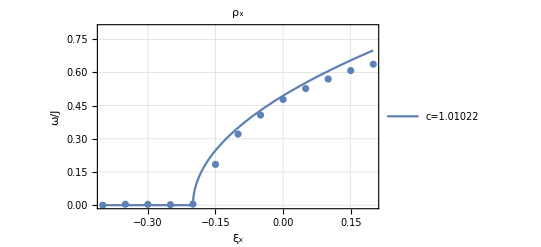

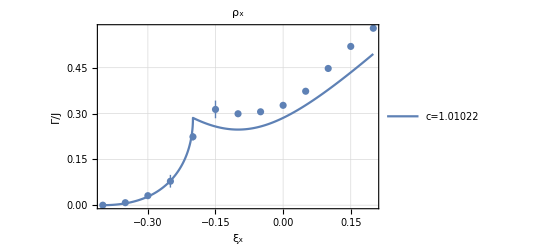

### Has ee

{0.190.090.09,0.0100.0080.008,0.0110.0070.007,0.0120.0080.008,0.070.060.06,0.2180.0120.012,0.32730.00160.0016,0.4090.0090.009,0.4800.0080.008,0.52970.00200.0020,0.57510.00160.0016,0.61380.00220.0022,0.64280.00210.0021}

{0.180.070.07,0.0520.0240.024,0.0880.0260.026,0.1540.0260.026,0.250.040.04,0.260.050.05,0.270.060.06,0.280.040.04,0.2990.0290.029,0.3470.0190.019,0.4220.0180.018,0.4980.0170.017,0.5590.0180.018}

{a→1.0000.0100.010}

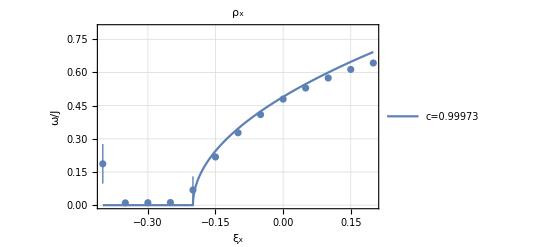

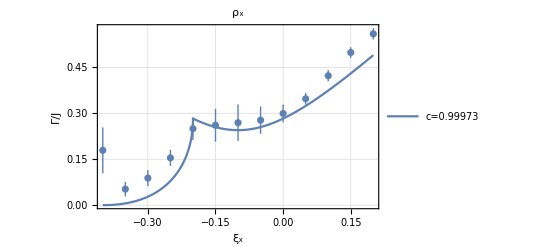

### has ee fitting is not correct